### Definitions

#### Translation check

```mathematica
(4 π^2)/(e^2 λ)v^2/Λ^2/.e->√(4π α)
```

(π v^2)/(α λ Λ^2)

```mathematica
(8 π^2)/(y λ)v^2/Λ^2/.π^2->π e^2/(4 α)/.y->e m/(√2 M sin)
```

(2 √2 e M π sin v^2)/(m α λ Λ^2)

#### Pheno expressions

```mathematica
test:={RK==1 + 0.23(c9me + c9pme) - 0.233(c10me+c10pme),
RKstl==0.92+0.07c9me-0.10c9pme-0.11c10me+0.11c10pme+0.55c7,
RKsl==1+0.20c9me-0.19c9pme-0.27c10me+0.21c10pme}
```

#### SMEFT → WET

```mathematica
C9[a_]:=π/(α λ)v^2/Λ^2(Clq1[a,a,2,3]+Clq3[a,a,2,3]+Cqe[2,3,a,a])
C10[a_]:=-π/(α λ)v^2/Λ^2(Clq1[a,a,2,3]+Clq3[a,a,2,3]-Cqe[2,3,a,a])
C9p[a_]:=π/(α λ)v^2/Λ^2(Cld[a,a,2,3]+Ced[a,a,2,3])
C10p[a_]:=-π/(α λ)v^2/Λ^2(Cld[a,a,2,3]-Ced[a,a,2,3])
```

```mathematica
values:={λ->-0.04114238998,Λ->1000,v->246,α->0.0072973525664}
```

```mathematica
π/(α λ)v^2/Λ^2/.values
```

-633.235

### Working scenarios

#### test I) only (C_lq^(1))_μμ23, i.e. C_9=-C_10. WORKS

```mathematica
subs:={c9me->C9[μ-e],c10me->C10[μ-e],Clq3[___]->0,Cqe[___]->0,c9pme->0,c10pme->0,c7->0};
```

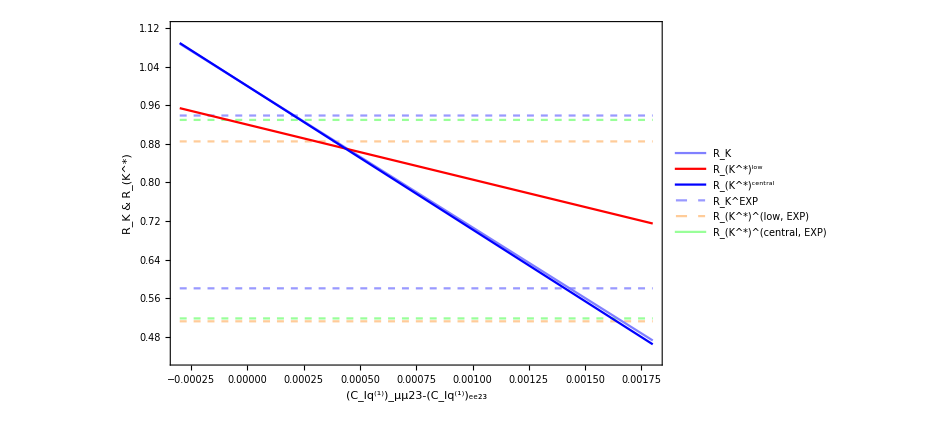

```mathematica
Plot[{0.745+2 √(0.09^2+0.036^2),0.745-2 √(0.074^2+0.036^2),0.660+2 √(0.110^2+0.024^2),0.660-2 √(0.070^2+0.024^2),0.685+2 √(0.113^2+0.047^2),0.685-2 √(0.069^2+0.047^2),test[[1,2]]//.subs/.values,test[[2,2]]//.subs/.values,test[[3,2]]//.subs/.values},{ Clq1[-e+μ,-e+μ,2,3],-0.00030,0.0018},PlotRange->{0.435,1.12},PlotLegends->LineLegend[{Lighter[Blue,0.5],Red,Blue,Directive[Lighter[Blue,.6],Dashed],Directive[Lighter[Orange,.6],Dashed],Directive[Lighter[Green,.6]]},{"R_K","R_(K^*)^low","R_(K^*)^central","R_K^EXP","R_(K^*)^(low,  EXP)","R_(K^*)^(central,  EXP)"}],PlotStyle->{Directive[Lighter[Blue,.6],Dashed],Directive[Lighter[Blue,.6],Dashed],Directive[Lighter[Orange,.6],Dashed],Directive[Lighter[Orange,.6],Dashed],Directive[Lighter[Green,.6],Dashed],Directive[Lighter[Green,.6],Dashed],Directive[Lighter[Blue,0.5],Thick],Directive[Red,Thick],Directive[Blue,Thick]},AxesLabel->{"(C_lq^(1))_μμ23-(C_lq^(1))_ee23","R_K & R_(K^*)"},Frame->True,ImageSize->700]
```

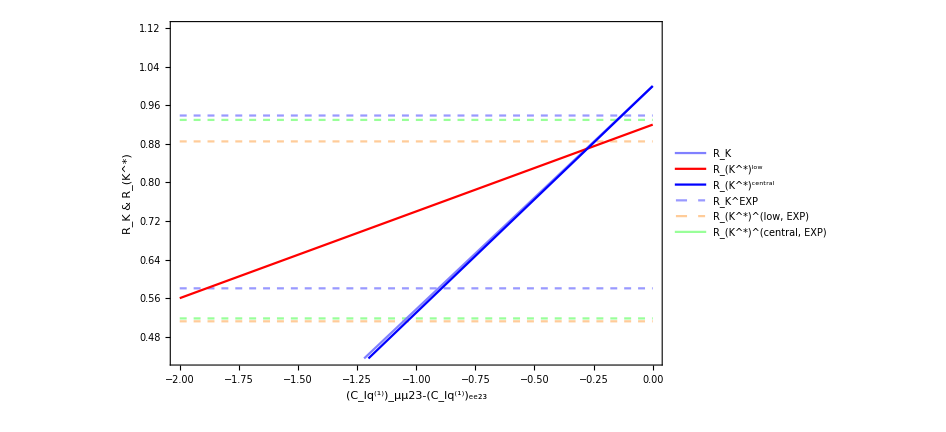

```mathematica
Plot[{0.745+2 √(0.09^2+0.036^2),0.745-2 √(0.074^2+0.036^2),0.660+2 √(0.110^2+0.024^2),0.660-2 √(0.070^2+0.024^2),0.685+2 √(0.113^2+0.047^2),0.685-2 √(0.069^2+0.047^2),test[[1,2]]/.Clq3[___]->0/.Cqe[___]->0/.c9pme->0/.c10me->-c9me/.c10pme->0/.c7->0/.values,test[[2,2]]/.Clq3[___]->0/.Cqe[___]->0/.c9pme->0/.c10me->-c9me/.c10pme->0/.c7->0/.values,test[[3,2]]/.Clq3[___]->0/.Cqe[___]->0/.c9pme->0/.c10me->-c9me/.c10pme->0/.c7->0/.values},{ c9me,-2,0},PlotRange->{0.435,1.12},PlotLegends->LineLegend[{Lighter[Blue,0.5],Red,Blue,Directive[Lighter[Blue,.6],Dashed],Directive[Lighter[Orange,.6],Dashed],Directive[Lighter[Green,.6]]},{"R_K","R_(K^*)^low","R_(K^*)^central","R_K^EXP","R_(K^*)^(low,  EXP)","R_(K^*)^(central,  EXP)"}],PlotStyle->{Directive[Lighter[Blue,.6],Dashed],Directive[Lighter[Blue,.6],Dashed],Directive[Lighter[Orange,.6],Dashed],Directive[Lighter[Orange,.6],Dashed],Directive[Lighter[Green,.6],Dashed],Directive[Lighter[Green,.6],Dashed],Directive[Lighter[Blue,0.5],Thick],Directive[Red,Thick],Directive[Blue,Thick]},AxesLabel->{"(C_lq^(1))_μμ23-(C_lq^(1))_ee23","R_K & R_(K^*)"},Frame->True,ImageSize->700]
```

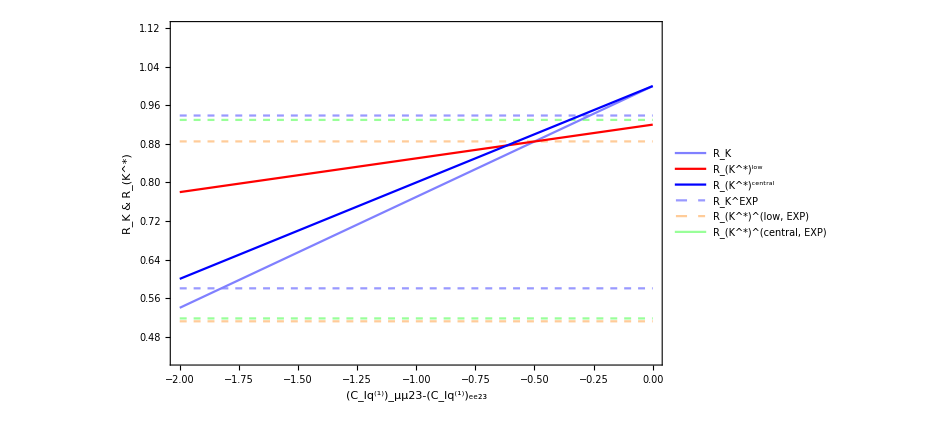

```mathematica
Plot[{0.745+2 √(0.09^2+0.036^2),0.745-2 √(0.074^2+0.036^2),0.660+2 √(0.110^2+0.024^2),0.660-2 √(0.070^2+0.024^2),0.685+2 √(0.113^2+0.047^2),0.685-2 √(0.069^2+0.047^2),test[[1,2]]/.Clq3[___]->0/.Cqe[___]->0/.c9pme->0/.c10me->0/.c10pme->0/.c7->0/.values,test[[2,2]]/.Clq3[___]->0/.Cqe[___]->0/.c9pme->0/.c10me->0/.c10pme->0/.c7->0/.values,test[[3,2]]/.Clq3[___]->0/.Cqe[___]->0/.c9pme->0/.c10me->0/.c10pme->0/.c7->0/.values},{ c9me,-2,0},PlotRange->{0.435,1.12},PlotLegends->LineLegend[{Lighter[Blue,0.5],Red,Blue,Directive[Lighter[Blue,.6],Dashed],Directive[Lighter[Orange,.6],Dashed],Directive[Lighter[Green,.6]]},{"R_K","R_(K^*)^low","R_(K^*)^central","R_K^EXP","R_(K^*)^(low,  EXP)","R_(K^*)^(central,  EXP)"}],PlotStyle->{Directive[Lighter[Blue,.6],Dashed],Directive[Lighter[Blue,.6],Dashed],Directive[Lighter[Orange,.6],Dashed],Directive[Lighter[Orange,.6],Dashed],Directive[Lighter[Green,.6],Dashed],Directive[Lighter[Green,.6],Dashed],Directive[Lighter[Blue,0.5],Thick],Directive[Red,Thick],Directive[Blue,Thick]},AxesLabel->{"(C_lq^(1))_μμ23-(C_lq^(1))_ee23","R_K & R_(K^*)"},Frame->True,ImageSize->700]
```

#### my test: only (C_lq^(1))_μμ23+(C_lq^(3))_μμ23+C_qe_(23μμ) = 0, i.e. C_9=0,C_10≠0. WORKS

```mathematica
subs:={c9me->C9[μ-e],c10me->C10[μ-e],Cqe[2,3,-e+μ,-e+μ]->- Clq1[-e+μ,-e+μ,2,3]- Clq3[-e+μ,-e+μ,2,3],c9pme->0,c10pme->0,c7->0};
```

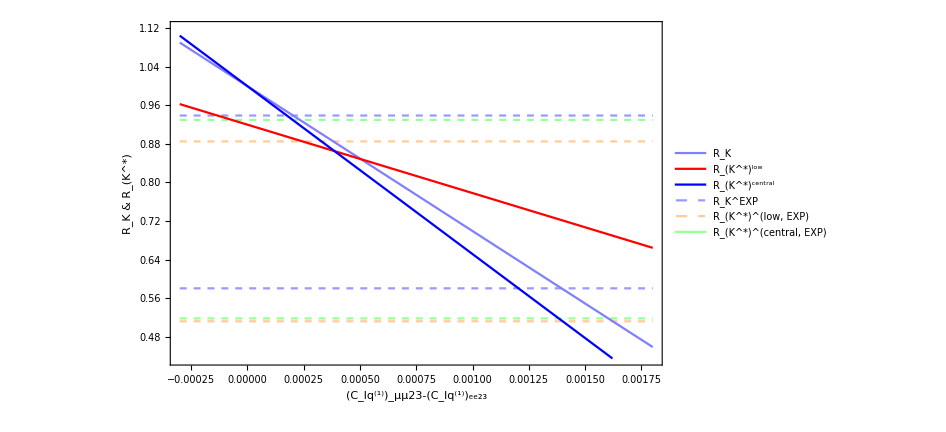

```mathematica
Plot[{0.745+2 √(0.09^2+0.036^2),0.745-2 √(0.074^2+0.036^2),0.660+2 √(0.110^2+0.024^2),0.660-2 √(0.070^2+0.024^2),0.685+2 √(0.113^2+0.047^2),0.685-2 √(0.069^2+0.047^2),test[[1,2]]//.subs/.Clq3[___]->0/.values,test[[2,2]]//.subs/.Clq3[___]->0/.values,test[[3,2]]//.subs/.Clq3[___]->0/.values},{ Clq1[-e+μ,-e+μ,2,3],-0.00030,0.0018},PlotRange->{0.435,1.12},PlotLegends->LineLegend[{Lighter[Blue,0.5],Red,Blue,Directive[Lighter[Blue,.6],Dashed],Directive[Lighter[Orange,.6],Dashed],Directive[Lighter[Green,.6]]},{"R_K","R_(K^*)^low","R_(K^*)^central","R_K^EXP","R_(K^*)^(low,  EXP)","R_(K^*)^(central,  EXP)"}],PlotStyle->{Directive[Lighter[Blue,.6],Dashed],Directive[Lighter[Blue,.6],Dashed],Directive[Lighter[Orange,.6],Dashed],Directive[Lighter[Orange,.6],Dashed],Directive[Lighter[Green,.6],Dashed],Directive[Lighter[Green,.6],Dashed],Directive[Lighter[Blue,0.5],Thick],Directive[Red,Thick],Directive[Blue,Thick]},AxesLabel->{"(C_lq^(1))_μμ23-(C_lq^(1))_ee23","R_K & R_(K^*)"},Frame->True,ImageSize->700]
```

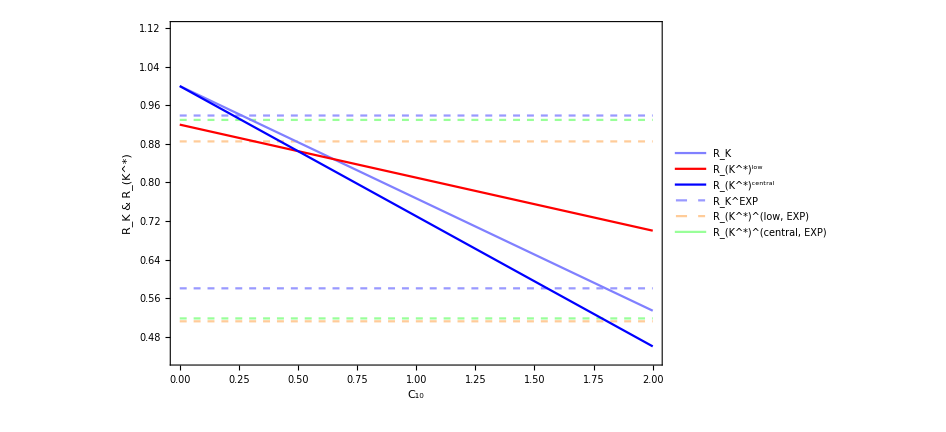

```mathematica
Plot[{0.745+2 √(0.09^2+0.036^2),0.745-2 √(0.074^2+0.036^2),0.660+2 √(0.110^2+0.024^2),0.660-2 √(0.070^2+0.024^2),0.685+2 √(0.113^2+0.047^2),0.685-2 √(0.069^2+0.047^2),test[[1,2]]/.Clq3[___]->0/.Cqe[___]->0/.c9pme->0/.c9me->0/.c10pme->0/.c7->0/.values,test[[2,2]]/.Clq3[___]->0/.Cqe[___]->0/.c9pme->0/.c9me->0/.c10pme->0/.c7->0/.values,test[[3,2]]/.Clq3[___]->0/.Cqe[___]->0/.c9pme->0/.c9me->0/.c10pme->0/.c7->0/.values},{ c10me,0,2},PlotRange->{0.435,1.12},PlotLegends->LineLegend[{Lighter[Blue,0.5],Red,Blue,Directive[Lighter[Blue,.6],Dashed],Directive[Lighter[Orange,.6],Dashed],Directive[Lighter[Green,.6]]},{"R_K","R_(K^*)^low","R_(K^*)^central","R_K^EXP","R_(K^*)^(low,  EXP)","R_(K^*)^(central,  EXP)"}],PlotStyle->{Directive[Lighter[Blue,.6],Dashed],Directive[Lighter[Blue,.6],Dashed],Directive[Lighter[Orange,.6],Dashed],Directive[Lighter[Orange,.6],Dashed],Directive[Lighter[Green,.6],Dashed],Directive[Lighter[Green,.6],Dashed],Directive[Lighter[Blue,0.5],Thick],Directive[Red,Thick],Directive[Blue,Thick]},AxesLabel->{"C_10","R_K & R_(K^*)"},Frame->True,ImageSize->700]
```

### Not working scenarios

#### only C_ld_μμ23, i.e. C'_9=-C'_10. DOES NOT WORK

```mathematica
subs:={c9pme->C9p[μ-e],c10pme->C10p[μ-e],Ced[___]->0,c9me->0,c10me->0,c7->0};
```

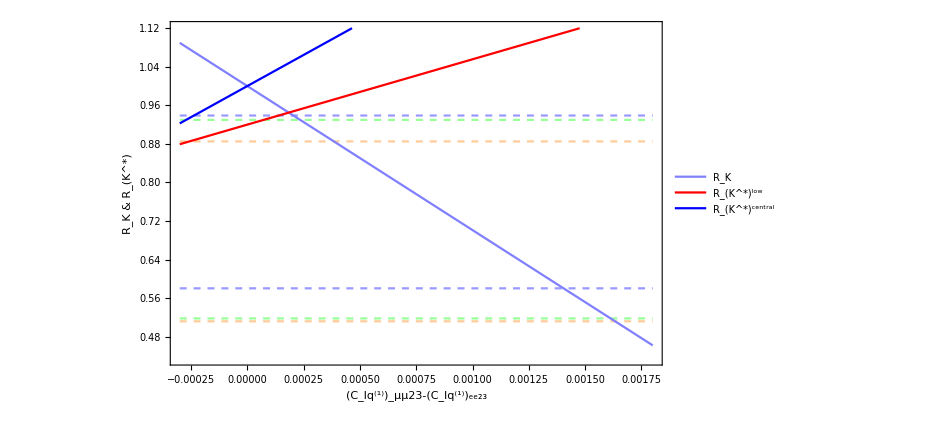

```mathematica
Plot[{0.745+2 √(0.09^2+0.036^2),0.745-2 √(0.074^2+0.036^2),0.660+2 √(0.110^2+0.024^2),0.660-2 √(0.070^2+0.024^2),0.685+2 √(0.113^2+0.047^2),0.685-2 √(0.069^2+0.047^2),test[[1,2]]//.subs/.values,test[[2,2]]//.subs/.values,test[[3,2]]//.subs/.values},{ Cld[-e+μ,-e+μ,2,3],-0.00030,0.0018},PlotRange->{0.435,1.12},PlotLegends->LineLegend[{Lighter[Blue,0.5],Red,Blue},{"R_K","R_(K^*)^low","R_(K^*)^central"}],PlotStyle->{Directive[Lighter[Blue,.6],Dashed],Directive[Lighter[Blue,.6],Dashed],Directive[Lighter[Orange,.6],Dashed],Directive[Lighter[Orange,.6],Dashed],Directive[Lighter[Green,.6],Dashed],Directive[Lighter[Green,.6],Dashed],Directive[Lighter[Blue,0.5],Thick],Directive[Red,Thick],Directive[Blue,Thick]},AxesLabel->{"(C_lq^(1))_μμ23-(C_lq^(1))_ee23","R_K & R_(K^*)"},Frame->True,ImageSize->700]
```

#### only C_ed_μμ23, i.e. C'_9=C'_10. DOES NOT WORK

```mathematica
subs:={c9pme->C9p[μ-e],c10pme->C10p[μ-e],Cld[___]->0,c9me->0,c10me->0,c7->0};
```

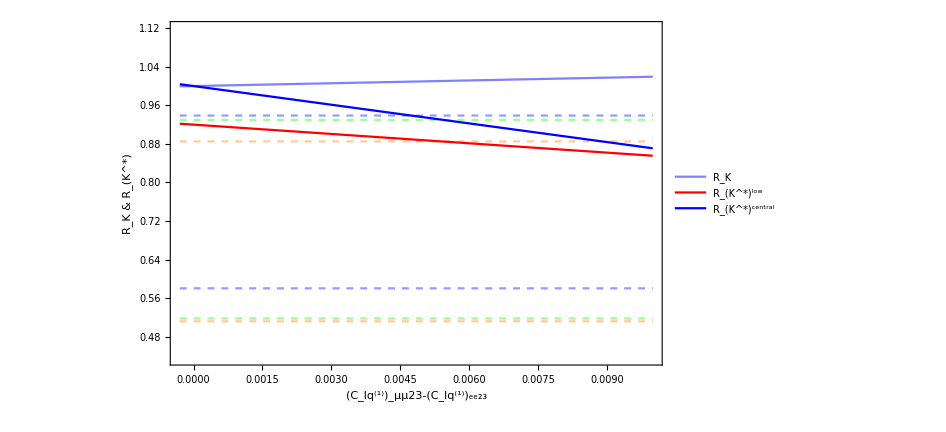

```mathematica
Plot[{0.745+2 √(0.09^2+0.036^2),0.745-2 √(0.074^2+0.036^2),0.660+2 √(0.110^2+0.024^2),0.660-2 √(0.070^2+0.024^2),0.685+2 √(0.113^2+0.047^2),0.685-2 √(0.069^2+0.047^2),test[[1,2]]//.subs/.values,test[[2,2]]//.subs/.values,test[[3,2]]//.subs/.values},{ Ced[-e+μ,-e+μ,2,3],-0.00030,0.01},PlotRange->{0.435,1.12},PlotLegends->LineLegend[{Lighter[Blue,0.5],Red,Blue},{"R_K","R_(K^*)^low","R_(K^*)^central"}],PlotStyle->{Directive[Lighter[Blue,.6],Dashed],Directive[Lighter[Blue,.6],Dashed],Directive[Lighter[Orange,.6],Dashed],Directive[Lighter[Orange,.6],Dashed],Directive[Lighter[Green,.6],Dashed],Directive[Lighter[Green,.6],Dashed],Directive[Lighter[Blue,0.5],Thick],Directive[Red,Thick],Directive[Blue,Thick]},AxesLabel->{"(C_lq^(1))_μμ23-(C_lq^(1))_ee23","R_K & R_(K^*)"},Frame->True,ImageSize->700]
```

#### only C_qe_(23μμ), i.e. C_9=C_10. DOES NOT WORK

```mathematica
subs:={c9me->C9[μ-e],c10me->C10[μ-e],Clq3[___]->0,Clq1[___]->0,c9pme->0,c10pme->0,c7->0};
```

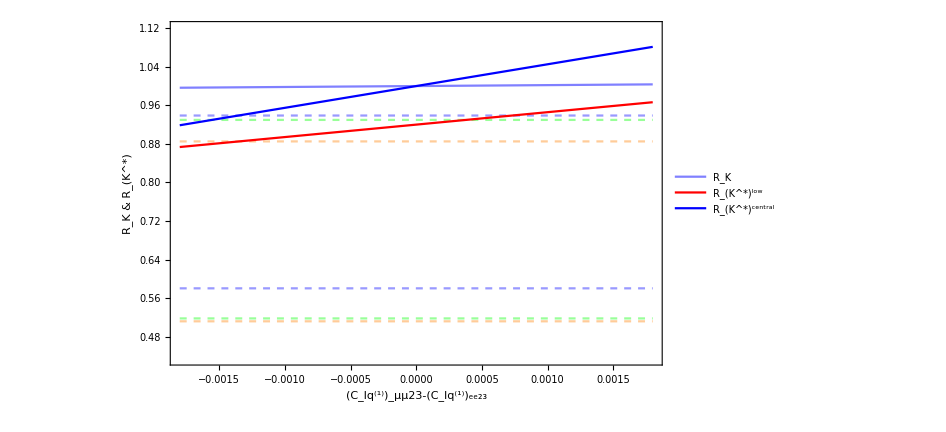

```mathematica
Plot[{0.745+2 √(0.09^2+0.036^2),0.745-2 √(0.074^2+0.036^2),0.660+2 √(0.110^2+0.024^2),0.660-2 √(0.070^2+0.024^2),0.685+2 √(0.113^2+0.047^2),0.685-2 √(0.069^2+0.047^2),test[[1,2]]//.subs/.values,test[[2,2]]//.subs/.values,test[[3,2]]//.subs/.values},{ Cqe[2,3,-e+μ,-e+μ],-0.0018,0.0018},PlotRange->{0.435,1.12},PlotLegends->LineLegend[{Lighter[Blue,0.5],Red,Blue},{"R_K","R_(K^*)^low","R_(K^*)^central"}],PlotStyle->{Directive[Lighter[Blue,.6],Dashed],Directive[Lighter[Blue,.6],Dashed],Directive[Lighter[Orange,.6],Dashed],Directive[Lighter[Orange,.6],Dashed],Directive[Lighter[Green,.6],Dashed],Directive[Lighter[Green,.6],Dashed],Directive[Lighter[Blue,0.5],Thick],Directive[Red,Thick],Directive[Blue,Thick]},AxesLabel->{"(C_lq^(1))_μμ23-(C_lq^(1))_ee23","R_K & R_(K^*)"},Frame->True,ImageSize->700]
```

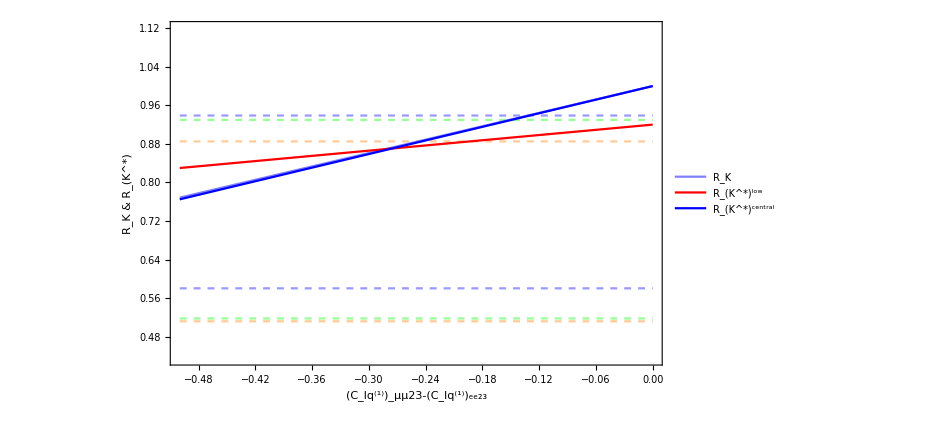

```mathematica
Plot[{0.745+2 √(0.09^2+0.036^2),0.745-2 √(0.074^2+0.036^2),0.660+2 √(0.110^2+0.024^2),0.660-2 √(0.070^2+0.024^2),0.685+2 √(0.113^2+0.047^2),0.685-2 √(0.069^2+0.047^2),test[[1,2]]/.Clq3[___]->0/.Cqe[___]->0/.c9pme->0/.c10me->-c9me/.c10pme->0/.c7->0/.values,test[[2,2]]/.Clq3[___]->0/.Cqe[___]->0/.c9pme->0/.c10me->-c9me/.c10pme->0/.c7->0/.values,test[[3,2]]/.Clq3[___]->0/.Cqe[___]->0/.c9pme->0/.c10me->-c9me/.c10pme->0/.c7->0/.values},{ c9me,-0.5,0},PlotRange->{0.435,1.12},PlotLegends->LineLegend[{Lighter[Blue,0.5],Red,Blue},{"R_K","R_(K^*)^low","R_(K^*)^central"}],PlotStyle->{Directive[Lighter[Blue,.6],Dashed],Directive[Lighter[Blue,.6],Dashed],Directive[Lighter[Orange,.6],Dashed],Directive[Lighter[Orange,.6],Dashed],Directive[Lighter[Green,.6],Dashed],Directive[Lighter[Green,.6],Dashed],Directive[Lighter[Blue,0.5],Thick],Directive[Red,Thick],Directive[Blue,Thick]},AxesLabel->{"(C_lq^(1))_μμ23-(C_lq^(1))_ee23","R_K & R_(K^*)"},Frame->True,ImageSize->700]
```

```mathematica
oldrange={0.753+1.96*0.09,0.753-1.96*0.09,0.680+1.96*0.093,0.680-1.96*0.093,0.707+1.96*0.102,0.707-1.96*0.102};
```

### Test for loops

#### Test

```mathematica
0.95/30^2/(-(y^2 λ)/(16 π^2)Log[Λ/μ])/.y->(√2 m)/v/.values/.μ->80.385/.m->173
```

1.65607